```mathematica
FabiusF::usage = "FabiusF[x] gives the value of the Fabius function F(x) for a non-negative real argument x.";
Macros`SetArgumentCount[FabiusF, 1];
SyntaxInformation[FabiusF] = {"ArgumentsPattern" -> {_}};
SetAttributes[FabiusF, {NumericFunction, Listable}];

Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &

(*https://mathematica.stackexchange.com/a/13245*)
powerOfTwoQ[n_] := IntegerQ[n] && BitAnd[n, n - 1] == 0

FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[0 <= Re[x] && Im[x] == 0, powerOfTwoQ[Denominator[x]], Message[FabiusF::realnn, x]; False] := iFabiusF[x]

ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);

tri[x_] := Piecewise[{{2 - x, x > 1}}, x]

iFabiusF[x_] := Module[{prec = Precision[x], s = 1, y = 0, z = SetPrecision[x, Infinity], n, p, q, tol, w}, z = If[0 <= z <= 2, tri[z], q = Quotient[z, 2];
        (*can replace ThueMorse[] with the implementation in https://mathematica.stackexchange.com/a/89351*)If[ThueMorse[q] == 1, s = -1]; tri[z - 2 q]];
    tol = 10^(-prec);
    While[z > 0, n = -Floor[RealExponent[z, 2]]; p = 2^n; z -= 1/p; w = 1;
      Do[w = ariasD[m] + p z w/(n - m + 1); p /= 2, {m, n}];
      y = w - y;
      If[Abs[w] < Abs[y] tol, Break[]]];
    SetPrecision[s Abs[y], prec]]
```

```mathematica
ClearAll[iCurvaturePlotHelper,CurvaturePlot]
iCurvaturePlotHelper[f_?(Head[#]=!=List&),{t_,tmin_,tmax_},{{x0_,y0_},θ0_},opts:OptionsPattern[]]:=Module[{sol,θ,x,y,if},
sol=NDSolve[{
θ'[t]==f,
x'[t]==Cos[θ[t]],
y'[t]==Sin[θ[t]],
θ[tmin]==θ0,
x[tmin]==x0,
y[tmin]==y0
},{x,y},{t,tmin,tmax},opts];
if={x[#],y[#]}&/.First[sol];
if
]
CurvaturePlot[f_,{t_,tmin_,tmax_},opts:OptionsPattern[]]:=CurvaturePlot[f,{t,tmin,tmax},{{0,0},0},opts]
CurvaturePlot[f_,{t_,tmin_,tmax_},p:{{x0_,y0_},θ0_},opts:OptionsPattern[]]:=Module[{θ,x,y,sol,rlsplot,rlsndsolve,if,ifs},
rlsplot=FilterRules[{opts},Options[ParametricPlot]];
rlsndsolve=FilterRules[{opts},Options[NDSolve]];
If[Head[f]===List,
ifs=iCurvaturePlotHelper[#,{t,tmin,tmax},p,Evaluate@(Sequence@@rlsndsolve)]&/@f;
ParametricPlot[Evaluate[#[tplot]&/@ifs],{tplot,tmin,tmax},Evaluate@(Sequence@@rlsplot)]
,
if=iCurvaturePlotHelper[f,{t,tmin,tmax},p,Evaluate@(Sequence@@rlsndsolve)];
ParametricPlot[Evaluate[if[tplot]],{tplot,tmin,tmax},Evaluate@(Sequence@@rlsplot)]
]
]
```

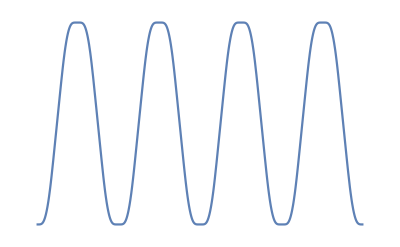
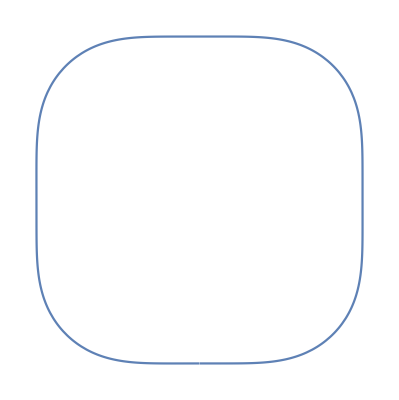

```mathematica
{
Plot[Piecewise[{{Abs[FabiusF[x*.6365]],x<2},{Abs[FabiusF[x*.6365]],x>2}}],{x,0,12.5625},Axes->False]
,
CurvaturePlot[Piecewise[{{Abs[FabiusF[x*.6365]],x<2},{Abs[FabiusF[x*.6365]],x>2}}],{x,0,12.5625},Axes->False]
}
```

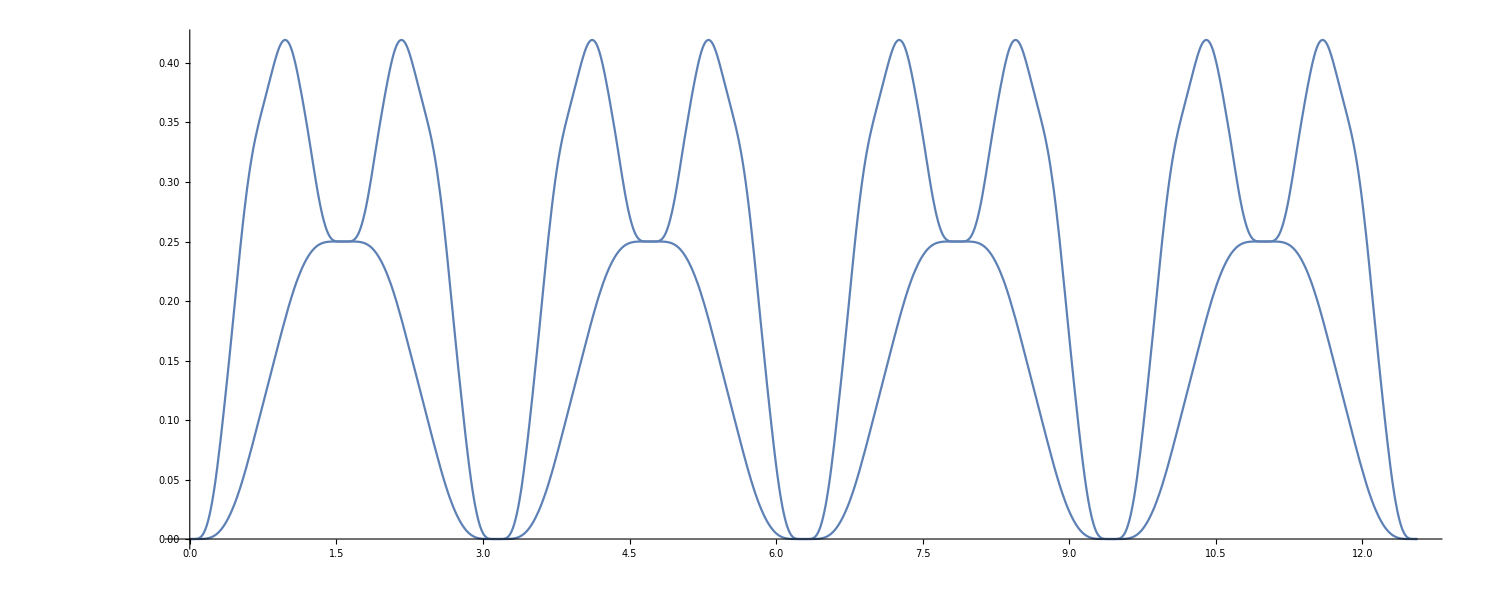

```mathematica
Show[
Plot[Abs[FabiusF[x*.6365]]*.25,{x,0,12.5625},Axes->True,PlotRange->Full,AspectRatio->Automatic]
,
Plot[(Abs[FabiusF[x*.6365]]*.25)+Abs[FabiusF'[x*.6365]]*.125,{x,0,12.5625},Axes->True,PlotRange->Full,AspectRatio->Automatic],PlotRange->Full]
```